{17.1,33.,17.1,16.5}

{7,6,7,8}

{1.22143,2.75,1.22143,1.03125}

20.747 % athlete profit

41.85 $ Nceno profit

3.4875 % of user stake per user per week $ Nceno profit

4.185 rev per user $ Nceno profit

1.04625 rev per user per week $ Nceno profit

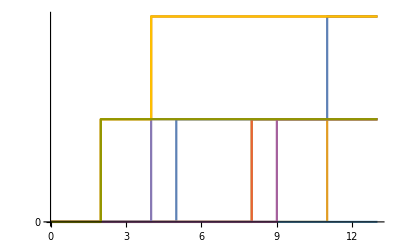

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
failRate = 0.1; (*failure rate*)
weeks = 6; (*in weeks*)
ses =3; (*days per week quota*)
ppl = 10;
lim =5; 
perc={{100,0,0,0,0,0,0,0,0,0,0,0},{31,69,0,0,0,0,0,0,0,0,0,0},{19,36,45,0,0,0,0,0,0,0,0,0},{16,15,30,39,0,0,0,0,0,0,0,0},{13,8,26,20,33,0,0,0,0,0,0,0},{11,8,12,24,18,28,0,0,0,0,0,0},{9,9,5,20,16,19,23,0,0,0,0,0},{8,9,4,11,19,11,21,19,0,0,0,0},{7,8,4,5,15,15,9,21,15,0,0,0},{6,7,5,3,10,16,10,9,20,13,0,0},{5,6,5,2,6,13,14,7,11,19,11,0},{5,6,6,3,3,9,13,10,6,12,18,10}};
cost = 10;

workout = Range[0,ses weeks,1];
misses= Range[0,ppl ses weeks,1];
players = RandomFunction[PoissonProcess[ failRate],{0,weeks ses,1},ppl];
data = Normal[players];
fails = Table[data[[All,(s+1),2]]-data[[All,(s),2]],{s,1,ses weeks}] ;(*fails is a set of workouts. Each workout is an array. Each index is a player. Each player is a failure count.*)
 
pot = Table[0,weeks];
(*table of lost stake by week... needs careful attention*)

strikes = Table[0,ppl];

winners =Table[0,weeks]; (*weekly winner count*)

For[p=1,p<ppl+1,p++,
For[w=1,w<weeks+1,w++,
If[strikes[[p]]<lim,
prevStrikes=strikes[[p]];
failSum=0;
For[x=(w-1)*ses+1,x<w*ses+1,x++,
failSum+=fails[[x,p]];
] ;
If[failSum==0,winners[[w]]++,
strikes[[p]]+=failSum;
For[f=prevStrikes+1,f<strikes[[p]]+1,f++,
pot[[w]]+=0.01*perc[[lim,f]]*cost*lim;
]
];
]
];
]


pot
winners
payouts = Table[0,weeks]; 
For[w=1,w<weeks+1,w++,
If[winners[[w]]>0,payouts[[w]]= 0.5*pot[[w]]/winners[[w]],
payouts[[w]]=0]
]

payouts 

100*(Sum[payouts[[i]],{i,1,weeks}]/(lim*cost))"% athlete profit"

ncenoPO = Table[0,weeks]; (*Nceno revenue*)
For[w=1,w<weeks+1,w++,
ncenoPO[[w]]= .5 pot[[w]]
]

ncenoProfit = Sum[ncenoPO[[i]],{i,1,weeks}] "$ Nceno profit"
100 ncenoProfit/(N[ppl*lim*cost*weeks]) "% of user stake per user per week"
ncenoProfit/(ppl) "rev per user"
ncenoProfit/(ppl*weeks) "rev per user per week"

ListStepPlot[players,Filling->None,Ticks->{workout,misses}, PlotRange->{{0,weeks ses+1},Automatic}]
fails;
MatrixForm[fails]
```